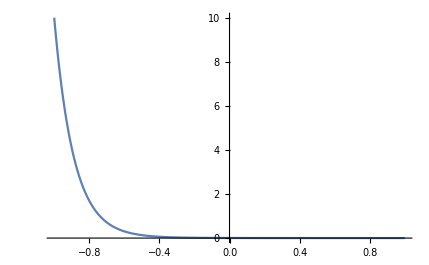

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```